# Baryon Code Tests

## Bjorken Tests

## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[ParentDirectory[wd]]
```

/Users/Lipei/Documents/GitHub/BEShydro/tests/Plotting

/Users/Lipei/Documents/GitHub/BEShydro

### constants

```mathematica
hbarc=0.197326938;
```

```mathematica
Nc=3;
Nf=2.5;
fac=3(2(Nc^2-1)+7/2Nc*Nf)Pi^2/90;
facT=fac^(1/4);
```

```mathematica
fac*3.05^4
```

1202.83

### plot styles

```mathematica
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[3],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[3],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};
```

```mathematica
FrameTicksFontSize=30;
FrameFontSize=30;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[AbsoluteThickness[1.1]],Directive[AbsoluteThickness[1.1]]},BaseStyle->{FontFamily->"Times",FontSize->30},AspectRatio->0.75,ImageSize->600,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
```

### data reader

```mathematica
Off[Interpolation::inhr];
varInt[t_,dir_,var_]:=Interpolation[Import[dir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{4,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

## Nonconformal Isreal-Stewart Bjorken with Baryon

### semi-analytical solution

#### equation of state

```mathematica
Clear[P,ed,cs2]
```

```mathematica
P[e_]:=(6.870405693362224*^-8 e^22+0.00008637928590991327 e^21+0.017119385861435455 e^20+0.3214239844038686 e^19-15.747028874943805 e^18+82.16248694648101 e^17+84.12461298404816 e^16+1856.978469728099 e^15+31589.159223138206 e^14-3885.4214706636 e^13+7686.326010247679 e^12-97503.39602753054 e^11+103763.15778408266 e^10-118748.3865513986 e^9+79207.98821000032 e^8-43581.50746943962 e^7+14982.941591340483 e^6-5094.798238346226 e^5+215.9010649614951 e^4-669.2491807056626 e^3-32.88537536711383 e^2-0.10459738246200945 e+7.65322437572353*^-6)/(-2.6458329653875896*^-13 e^22+2.116259364992001*^-7 e^21+0.00027905595468488936 e^20+0.06077200347319396 e^19+1.7149149650310491 e^18-54.58410395809249 e^17-25.027803854419638 e^16+3091.1142974187396 e^15-7645.676914092535 e^14+289396.9261750485 e^13-72928.01964690415 e^12-167022.021198068 e^11-114927.36007725315 e^10-57627.99954667258 e^9-26798.0052522393 e^8-14023.459737628238 e^7-8302.100168065315 e^6-5855.999552921422 e^5-3888.658475265885 e^4-5182.711489765338 e^3-2642.4360129388488 e^2-133.04514102258597 e-0.5169116846760041)
Tint[e_]:=(-4.873400811469563*^-10-0.33967898165285937 e-243.87315076666465 e^2-7950.4417656525575 e^3-15830.731725359203 e^4-1638.2165592489832 e^5-15.708990537469983 e^6-0.017506852476184522 e^7-1.836593645164133*^-6 e^8)/(-4.873378567876981*^-6-1.9735695129421675 e-691.5144322242182 e^2-13185.130839434429 e^3-20098.669864541644 e^4-1169.8522357611525 e^5-6.630649855145946 e^6-0.004312673981317225 e^7-2.1655522622011757*^-7 e^8)
ed[T_]:=(-0.011958188410851651+119.89423098138208 T-3156.9475699248055 T^2+32732.86844374939 T^3-187899.8994764422 T^4+712537.3610845465 T^5-1.557049803609345*^6 T^6+1.4852519861308339*^6 T^7+532132.6079941876 T^8-1.963099445042592*^6 T^9-4484.44579242679 T^10+1.7984228830058286*^6 T^11+119345.25619517374 T^12-1.3499773937058165*^6 T^13-207838.4995663606 T^14+654970.2138652403 T^15-78643.00334616247 T^16+40274.00078068926 T^17+422619.58977657766 T^18-409688.07836393174 T^19-62005.75915066359 T^20+46788.14270090656 T^21+40784.330477857235 T^22-12589.47744840392 T^23)/(31630.074365558292-127100.88940643385 T+173528.1225422275 T^2-39403.297956865215 T^3-85582.57873541754 T^4+9320.560804233442 T^5+50882.74198960172 T^6+20335.926473421183 T^7-14897.725710713818 T^8-23836.484117457 T^9-13726.013896090335 T^10+4517.908673107615 T^11+18056.19917986404 T^12+14954.82860467155 T^13+2569.623976952738 T^14-9304.046211514986 T^15-15606.429173842751 T^16+8383.710735812094 T^17+1591.3177623932843 T^18-678.748230997762 T^19-33.58687934953277 T^20+3.2520554133126285 T^21-0.19647288043440464 T^22+0.005443394551264717 T^23)
cs2[e_]:=(1.2625814949136498*^-42+2.4439030393295734*^-33 e+9.322641344497548*^-26 e^2+1.9540661873302495*^-19 e^3+5.0244280894342345*^-14 e^4+2.369176131226614*^-9 e^5+0.00002467595835925649 e^6+0.0608709022174928 e^7+35.13582886022962 e^8+4222.887394189519 e^9+72483.09074617726 e^10+417317.67297479673 e^11+585334.4710663276 e^12+57539.2198687339 e^13+14441.972045822631 e^14+1216.0067118006687 e^15+13.489236656837132 e^16+14.786577881305382 e^17-2.5565796031645758 e^18+0.05603218920634199 e^19+0.000984102224155054 e^20+2.1161830800816893*^-6 e^21+8.101199742688298*^-10 e^22+3.89552175647867*^-14 e^23)/(3.56558833745313*^-41+4.6403916630291216*^-32 e+1.246926715508643*^-24 e^2+1.9406804331642527*^-18 e^3+3.8792079821435393*^-13 e^4+1.473941085930358*^-8 e^5+0.0001283715493908053 e^6+0.27578987407916083 e^7+144.29417387657588 e^8+16436.520976883963 e^9+315466.19533599314 e^10+2.8901807318940037*^6 e^11+5.506960426273549*^6 e^12-355776.5733809447 e^13+156209.84678369848 e^14-5701.991686556281 e^15+832.8660760210314 e^16+1.9784144986425583 e^17-7.706332342730179 e^18+0.20216864185984038 e^19+0.00313721024057907 e^20+6.541440626577012*^-6 e^21+2.4689937881750025*^-9 e^22+1.1758507795621395*^-13 e^23)
```

#### bulk viscous pressure transport coefficients

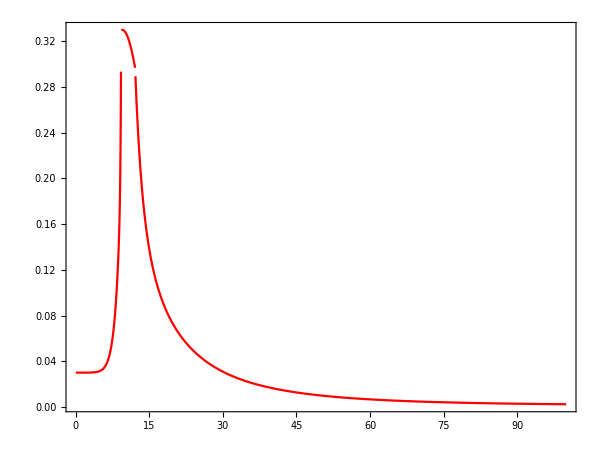

```mathematica
A1=-13.77;
A2=27.55;
A3=13.45;
lambda1=0.9;
lambda2=0.25;
lambda3=0.9;
lambda4=0.22;
sigma1=0.025;
sigma2=0.13;
sigma3=0.0025;
sigma4=0.022;
zetabar[e_]:=Piecewise[{{lambda1*Exp[-(Tint[e]/1.01355-1)/sigma1]+lambda2*Exp[-(Tint[e]/1.01355-1)/sigma2]+0.001,Tint[e]/1.01355>=1.05},{lambda3*Exp[(Tint[e]/1.01355-1)/sigma3]+lambda4*Exp[(Tint[e]/1.01355-1)/sigma4]+0.03,Tint[e]/1.01355<=0.995},{A1*(Tint[e]/1.01355)^2+A2*Tint[e]/1.01355-A3,Tint[e]/1.01355>=0.995&&Tint[e]/1.01355<=1.05}}];
Plot[zetabar[e],{e,0.001,100},PlotRange->All,PlotStyle->Red]
```

```mathematica
betaPi[e_]:=15(1/3-cs2[e])^2(e+P[e])
lambdaPipi[e_]:=8(1/3-cs2[e])/5
tauPiInv[e_]:=15(1/3-cs2[e])^2Tint[e]/zetabar[e];
deltaPiPi=0.666667;
```

#### shear stress tensor transport coefficients

```mathematica
etabar=0.2;
betapi[e_]:=(e+P[e])/5;
taupiInv[e_]:=Tint[e]/5/etabar;
deltapipi=1.33333;
taupipi=1.42857;
lambdapiPi=1.2;
```

#### baryon diffusion transport coefficients

```mathematica
Cb=4.0;
taun[e_]=Cb/Tint[e];
deltann=1.0;
lambdann=0.6;
```

#### initial condition

```mathematica
t0=0.25;
tf=10;
```

```mathematica
n0=500;
neta0=10;
```

```mathematica
T0=4.5;
e0=ed[T0]
pizz0=4/(3*t0)*etabar*(e0+P[e0])/T0 (*pizz=-t*t*π^ηη*)(*pizz0/t0/t0*)
Pi0=0;(*-zetabar[e0]*(e0+P[e0])/T0/t0*)
```

5391.17

1690.79

#### equations of motion

```mathematica
Clear[e,pi,pizz,n,neta,edExact,piExact,pizzExact,nExact,netaExact]
```

```mathematica
eqs={D[e[t],t]==-(e[t]+P[e[t]]+pi[t]-pizz[t])/t,D[pi[t],t]==-pi[t]tauPiInv[e[t]]-betaPi[e[t]]/t-deltaPiPi*pi[t]/t+lambdaPipi[e[t]]pizz[t]/t,D[pizz[t],t]==-pizz[t]taupiInv[e[t]]+betapi[e[t]](4/3/t)-(taupipi/3+deltapipi)*pizz[t]/t+2*lambdapiPi*pi[t]/3/t,D[n[t],t]==-n[t]/t,
D[neta[t],t]==-neta[t]/taun[e[t]]-(1+deltann+2/3*lambdann)*neta[t]/t};
initcond={e[t0]==e0,pi[t0]==Pi0,pizz[t0]==pizz0,n[t0]==n0,neta[t0]==neta0};
{edExact,piExact,pizzExact,nExact,netaExact}={e,pi,pizz,n,neta}/.NDSolve[Join[eqs,initcond],{e,pi,pizz,n,neta},{t,t0,tf}][[1]];
```

#### plots

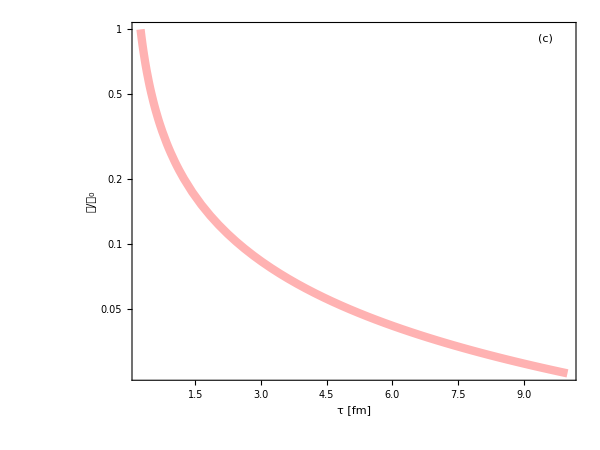

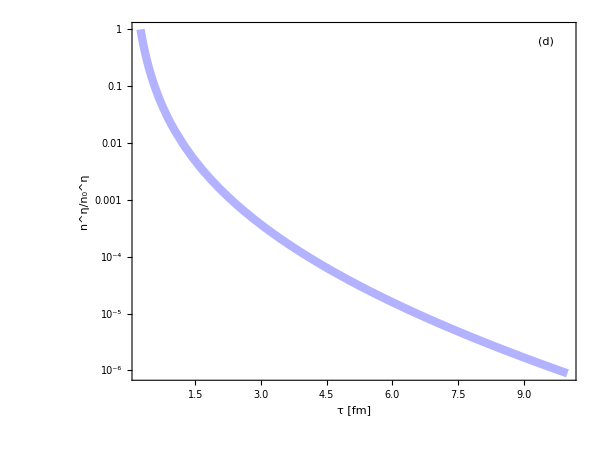

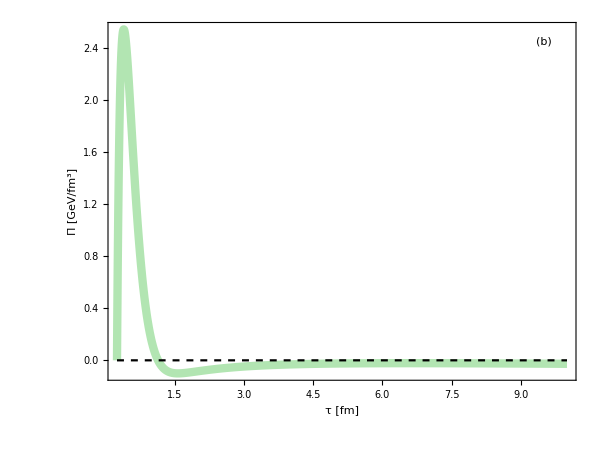

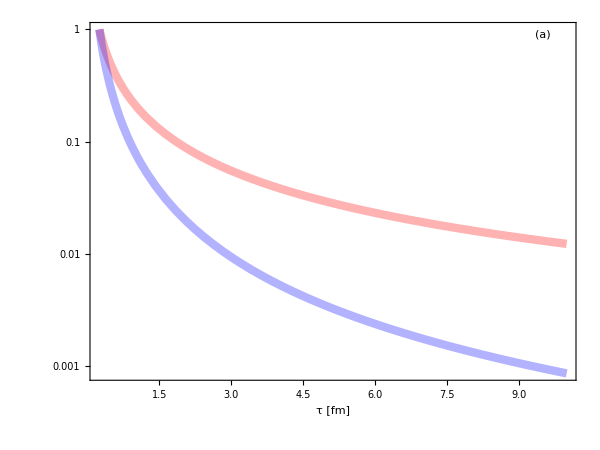

```mathematica
nplot=LogPlot[{nExact[t]/n0},{t,t0,tf},PlotRange->All,PlotStyle->{AbsoluteThickness[6],Red,Opacity[0.3]},FrameLabel->{"τ [fm]","𝒩/𝒩_0"},Epilog->Inset["(c)",{9.5,-0.1}],ImagePadding->{{115,20},{80,10}}]
netaplot=LogPlot[{netaExact[t]/neta0},{t,t0,tf},PlotRange->All,PlotStyle->{AbsoluteThickness[6],Blue,Opacity[0.3]},FrameLabel->{"τ [fm]","n^η/n_0^η"},Epilog->Inset["(d)",{9.5,-0.5}],ImagePadding->{{115,20},{80,10}}]
piplot=Plot[{piExact[t],0.0},{t,t0,tf},PlotRange->All,PlotStyle->{{AbsoluteThickness[6],Darker[Green],Opacity[0.3]},{Dashed,Black}},FrameLabel->{"τ [fm]","Π [GeV/fm^3]"},Epilog->Inset["(b)",{9.5,2.45}],ImagePadding->{{115,20},{0,10}}]
epizzplot=LogPlot[{edExact[t]/e0,pizzExact[t]/pizz0},{t,t0,tf},PlotRange->All,PlotStyle->{{AbsoluteThickness[6],Red,Opacity[0.3]},{AbsoluteThickness[6],Blue,Opacity[0.3]}},FrameLabel->{"τ [fm]"},Epilog->Inset["(a)",{9.5,-0.1}],ImagePadding->{{115,20},{0,10}}]
```

### load numerical data

```mathematica
tlist=Table[t,{t,0.25,10.00,.01}];
```

```mathematica
outputDir=root<>"/output";
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
Clear[eInt,pinnInt,PiInt,nInt,netaInt];
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,pinnInt,PiInt,nInt,netaInt},{"e","pinn","pi","rhob","nbn"}}];
```

```mathematica
eTable=Table[{tlist[[i]],eInt[i-1][0,0,0]/eInt[0][0,0,0]},{i,1,Length[tlist]}];
pinnTable=Table[{tlist[[i]],-tlist[[i]]*tlist[[i]]*pinnInt[i-1][0,0,0]/(-tlist[[1]]*tlist[[1]]*pinnInt[0][0,0,0])},{i,1,Length[tlist]}];
PiTable=Table[{tlist[[i]],PiInt[i-1][0,0,0]},{i,1,Length[tlist]}];
nTable=Table[{tlist[[i]],nInt[i-1][0,0,0]/nInt[0][0,0,0]},{i,1,Length[tlist]}];
netaTable=Table[{tlist[[i]],netaInt[i-1][0,0,0]/netaInt[0][0,0,0]},{i,1,Length[tlist]}];
```

```mathematica
epinnnPlot=ListLogPlot[{eTable,pinnTable},Joined->True,PlotStyle->{{AbsoluteThickness[2],Red,Dashing[Large]},{AbsoluteThickness[2],Blue,Dashing[Large]}},PlotLegends->Placed[LineLegend[{{"ℰ/ℰ_0","π/π_0"}},LabelStyle-> {FontSize->30,FontFamily->"Times"},LegendMarkerSize->{{30,10}}],{0.7,0.8}]];
pinPlot=ListLinePlot[PiTable,Joined->True,PlotRange->All,PlotStyle->{AbsoluteThickness[2],Darker[Green],Dashing[Large]}];
nnPlot=ListLogPlot[nTable,Joined->True,PlotStyle->{AbsoluteThickness[2],Red,Dashing[Large]}];
netanPlot=ListLogPlot[netaTable,Joined->True,PlotStyle->{AbsoluteThickness[2],Blue,Dashing[Large]}];
```

### make plots

```mathematica
epiplotcompare=Show[epizzplot,epinnnPlot];
piplotcompare=Show[piplot,pinPlot];
netaplotcompare=Show[netaplot,netanPlot];
nplotcompare=Show[nplot,nnPlot];
```

```mathematica
Export["IS_Bjorken_n.pdf",nplotcompare,ImageResolution->200]
Export["IS_Bjorken_neta.pdf",netaplotcompare,ImageResolution->200]
Export["IS_Bjorken_pi.pdf",piplotcompare,ImageResolution->200]
Export["IS_Bjorken_epizz.pdf",epiplotcompare,ImageResolution->200]
```

IS_Bjorken_n.pdf

IS_Bjorken_neta.pdf

IS_Bjorken_pi.pdf

IS_Bjorken_epizz.pdf

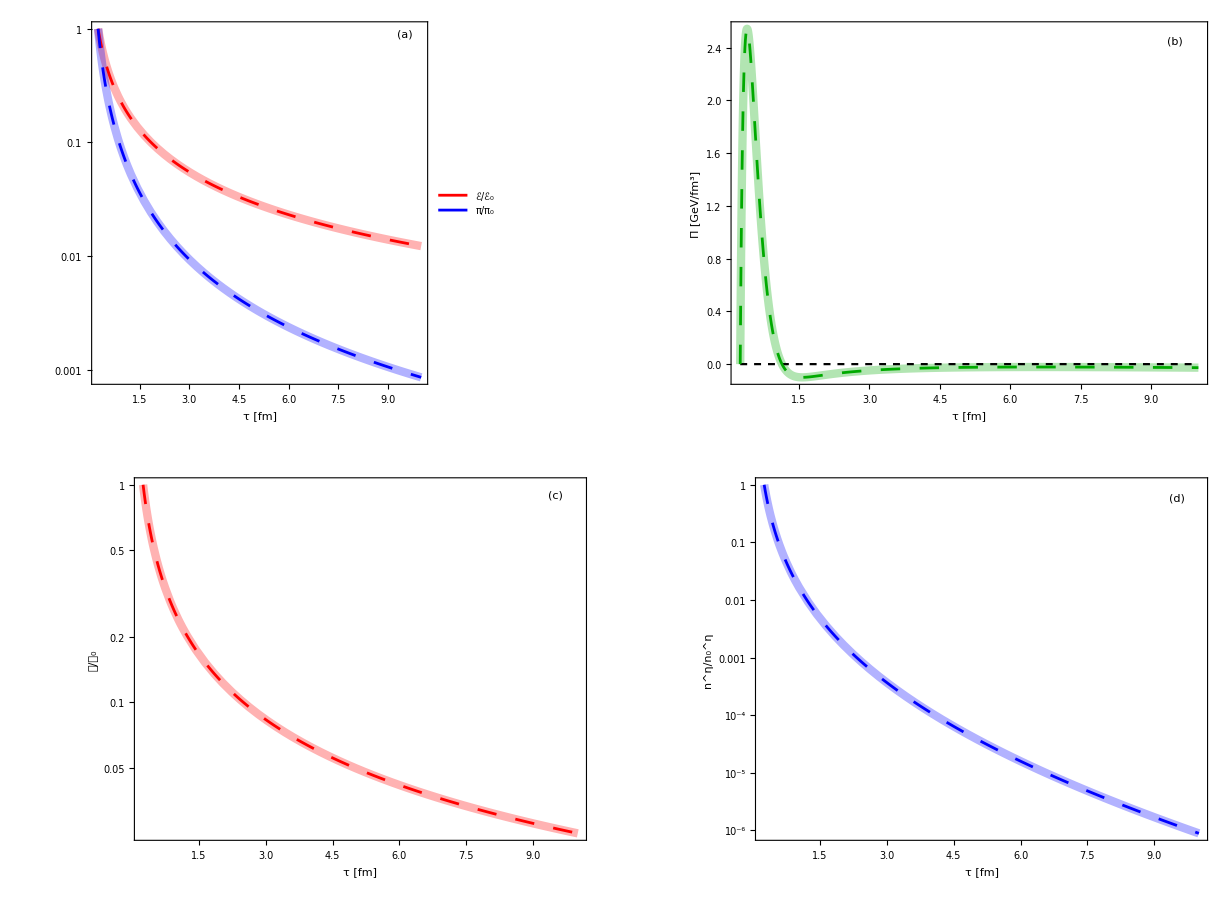

Bjorken_test.pdf

```mathematica
BjorkenIS=GraphicsGrid[{{epiplotcompare,piplotcompare},{nplotcompare,netaplotcompare}},Spacings->{10, 0}]
Export["Bjorken_test.pdf",BjorkenIS,ImageResolution->200]
```